```mathematica
showUniverse[universe,tiles,{6,1},visualUniverse]//ArrayPlot
```

-Graphics-

```mathematica
Position[Erosion[universe,1]-Erosion[universe,2],1]
```

{{1,4},{1,7},{2,4},{2,7},{3,4},{3,7},{3,8},{3,9},{3,10},{4,4},{4,10},{5,1},{5,2},{5,3},{5,4},{5,10},{6,1},{6,2},{6,3},{6,4},{6,10},{7,4},{7,10},{8,4},{8,10},{9,4},{9,10},{10,4},{10,10},{11,4},{11,10},{12,4},{12,10},{13,4},{13,10},{14,4},{14,10},{14,11},{14,12},{15,4},{15,10},{15,11},{15,12},{16,4},{16,10},{17,4},{17,5},{17,6},{17,7},{17,10},{18,7},{18,10},{19,7},{19,10},{20,7},{20,10},{21,7},{21,10},{22,6},{22,7},{22,8},{22,9},{22,10}}

```mathematica
trygrowUniverse[universe,tiles,{10,17}]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{Indeterminate,0}

```mathematica
growUniverse[universe,tiles,{10,17},visualUniverse]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

$Aborted

```mathematica
dimension=Ceiling[1.5*(First/@Dimensions/@tiles//Max)];
```

```mathematica
usedrange=usedRange[universe];
```

```mathematica
usedrange
```

{{1,16},{1,26}}

```mathematica
overlay[universe,usedrange]
```

-Graphics-

```mathematica
ibound=innerBound[universe];
```

```mathematica
ibound
```

8

```mathematica
spaced=takeUniverse[universe,{10,17},{dimension,dimension}];
```

```mathematica
spaced//ArrayPlot
```

-Graphics-

```mathematica
addNextTile[spaced,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

```mathematica
regiontoscan=scanRange[tile,spaced]
```

{{1,5},{1,11}}

```mathematica
overlay[spaced,regiontoscan]
```

-Graphics-

```mathematica
scores=Transpose[Table[score[addTile[tile,spaced,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]]
```

{{∞,∞,60,∞,80},{∞,∞,∞,∞,80},{∞,∞,∞,∞,80},{∞,∞,∞,∞,∞},{∞,∞,∞,∞,80},{∞,∞,∞,∞,88},{∞,∞,∞,∞,96},{∞,∞,78,91,104},{∞,70,84,98,112},{∞,75,90,105,120},{64,80,96,112,128}}

```mathematica
tile=tiles[[9]]
```

{{1,0,0,1},{1,1,1,1},{0,1,1,0},{0,1,1,0},{1,1,1,1},{1,0,0,1}}

```mathematica
tile//ArrayPlot
```

-Graphics-

```mathematica
scoresImg=Transpose[Table[scoreImg[addTile[tile,spaced,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

{{0.552941,0.552941,0.52549,0.552941,0.439216},{0.552941,0.552941,0.552941,0.552941,0.443137},{0.552941,0.552941,0.552941,0.552941,0.447059},{0.552941,0.552941,0.552941,0.486275,0.431373},{0.552941,0.552941,0.552941,0.552941,0.411765},{0.552941,0.552941,0.552941,0.552941,0.384314},{0.552941,0.552941,0.552941,0.552941,0.364706},{0.552941,0.388235,0.376471,0.360784,0.337255},{0.552941,0.345098,0.337255,0.333333,0.32549},{0.552941,0.32549,0.32549,0.321569,0.317647},{0.317647,0.317647,0.317647,0.317647,0.317647}}

```mathematica
(1-scoresImg)
```

{{0.447059,0.447059,0.47451,0.447059,0.560784},{0.447059,0.447059,0.447059,0.447059,0.556863},{0.447059,0.447059,0.447059,0.447059,0.552941},{0.447059,0.447059,0.447059,0.513725,0.568627},{0.447059,0.447059,0.447059,0.447059,0.588235},{0.447059,0.447059,0.447059,0.447059,0.615686},{0.447059,0.447059,0.447059,0.447059,0.635294},{0.447059,0.611765,0.623529,0.639216,0.662745},{0.447059,0.654902,0.662745,0.666667,0.67451},{0.447059,0.67451,0.67451,0.678431,0.682353},{0.682353,0.682353,0.682353,0.682353,0.682353}}

```mathematica
Max[Cases[Flatten[scores],_Integer]]
```

128

```mathematica
scores=scores/Max[Cases[Flatten[scores],_Integer]]*(1-scoresImg)//MatrixForm
```

(∞ | ∞ | 0.222426 | ∞ | 0.35049
∞ | ∞ | ∞ | ∞ | 0.348039
∞ | ∞ | ∞ | ∞ | 0.345588
∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | 0.367647
∞ | ∞ | ∞ | ∞ | 0.423284
∞ | ∞ | ∞ | ∞ | 0.476471
∞ | ∞ | 0.379963 | 0.454442 | 0.53848
∞ | 0.35815 | 0.434926 | 0.510417 | 0.590196
∞ | 0.395221 | 0.474265 | 0.556526 | 0.639706
0.341176 | 0.426471 | 0.511765 | 0.597059 | 0.682353)

```mathematica
newPos=Reverse[First[Take[Position[scores,Min[scores]],1]]]+First/@regiontoscan-{1,1}
```

{3,1}

```mathematica
minScores={};
```

```mathematica
AppendTo[minScores,{Min[scores],addTile[tile,spaced,newPos]}];
```

```mathematica
minScores
```

{{(∞ | ∞ | 0.222426 | ∞ | 0.35049
∞ | ∞ | ∞ | ∞ | 0.348039
∞ | ∞ | ∞ | ∞ | 0.345588
∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | 0.367647
∞ | ∞ | ∞ | ∞ | 0.423284
∞ | ∞ | ∞ | ∞ | 0.476471
∞ | ∞ | 0.379963 | 0.454442 | 0.53848
∞ | 0.35815 | 0.434926 | 0.510417 | 0.590196
∞ | 0.395221 | 0.474265 | 0.556526 | 0.639706
0.341176 | 0.426471 | 0.511765 | 0.597059 | 0.682353),{{1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}}

```mathematica
First[SortBy[minScores,#[[1]]&]][[2]]
```

{{1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
trygrowUniverse[universe,tiles,{10,17}]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

{28.4706,{{1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}

```mathematica
dimension=Ceiling[1.5*(First/@Dimensions/@tiles//Max)];
```

```mathematica
usedrange=usedRange[universe];
```

```mathematica
ibound=innerBound[universe];
```

```mathematica
spaced=takeUniverse[universe,{10,17},{dimension,dimension}];
```

```mathematica
spaced//ArrayPlot
```

-Graphics-

```mathematica
addNextTilewCost[spaced,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

{2.84706,{{1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}

```mathematica
SetSharedVariable[minMinScores];
minMinScores={};
Map[
offset=#;
AppendTo[minMinScores,trygrowUniverse[universe,tiles,offset]];
&,
Position[Erosion[universe,1]-Erosion[universe,2],1]
]
First[SortBy[minMinScores,#[[1]]&]][[2]]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

$Aborted

First::nofirst: {} has zero length and no first element.

Part::partw: Part 2 of First[{}] does not exist.

First[{}]⟦2⟧

```mathematica
Erosion[space2,1]-Erosion[space2,2]//ArrayPlot
```

-Graphics-

```mathematica
Position[Erosion[universe,1]-Erosion[universe,2],1]
```

{{1,4},{1,7},{2,4},{2,7},{3,4},{3,7},{3,8},{3,9},{3,10},{4,4},{4,10},{5,1},{5,2},{5,3},{5,4},{5,10},{6,1},{6,2},{6,3},{6,4},{6,10},{7,4},{7,10},{8,4},{8,10},{9,4},{9,10},{10,4},{10,10},{11,4},{11,10},{12,4},{12,10},{13,4},{13,10},{14,4},{14,10},{14,11},{14,12},{15,4},{15,10},{15,11},{15,12},{16,4},{16,10},{17,4},{17,5},{17,6},{17,7},{17,10},{18,7},{18,10},{19,7},{19,10},{20,7},{20,10},{21,7},{21,10},{22,6},{22,7},{22,8},{22,9},{22,10}}

```mathematica
space2//ArrayPlot
```

-Graphics-

```mathematica
spaceInitial=space;
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

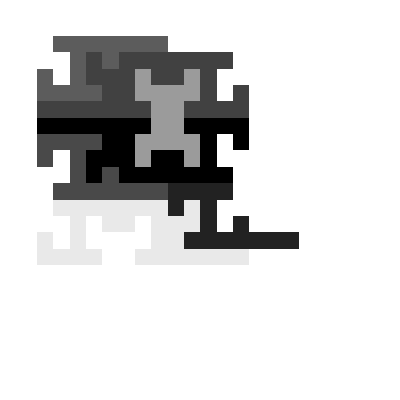

```mathematica
addNextTileLocal[]
```

```mathematica
Erosion[space,1]-Erosion[space,2]//ArrayPlot
```

-Graphics-

```mathematica
universe2=Table[0,{50},{50}];visualuniverse2=Table[0,{50},{50}];
```

```mathematica
putUniverse[universe2,space,{1,1}]
```

-Graphics-

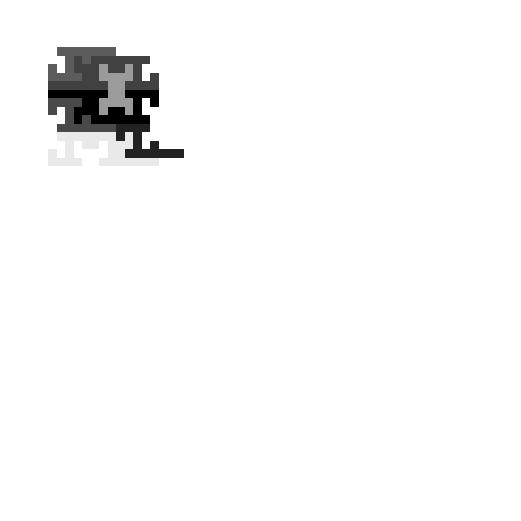

```mathematica
putUniverse[visualuniverse2,visualSpace,{1,1}]
```

```mathematica
ArrayPlot[universe2]
```

-Graphics-

```mathematica
1-EdgeDetect[Image[universe2,"Bit"]]
```

-Graphics-

```mathematica
Erosion[universe2,1]-Erosion[universe2,2]//ArrayPlot
```

-Graphics-

```mathematica
SetSharedVariable[minMinScores];
minMinScores={};
Map[
offset=#;
AppendTo[minMinScores,trygrowUniverse[universe2,tiles,offset]];
&,
Position[Erosion[universe2,1]-Erosion[universe2,2],1]
]
First[SortBy[minMinScores,#[[1]]&]][[2]]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

{{1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
ArrayPlot[{{1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}]
```

-Graphics-

```mathematica
space2//ArrayPlot
```

-Graphics-

```mathematica
space//ArrayPlot
```

-Graphics-

```mathematica
putUniverse[universe2,space,{1,1}]
```

-Graphics-

```mathematica
takenspace=takeUniverse[universe2,{10,6},{10,10}]
```

{{1,1,1,1,0,0,0,0,0,0},{1,1,0,1,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0},{1,1,0,1,0,0,0,0,0,0},{1,1,1,1,1,1,1,0,0,0},{1,1,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

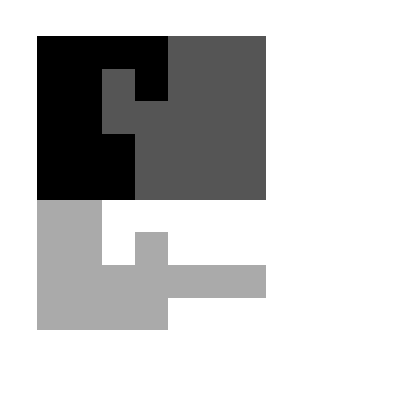

```mathematica
overlay[takenspace,regiontoscan]
```

```mathematica
tile=tiles[[9]];
regiontoscan=scanRange[tile,takenspace];
scores=Transpose[Table[score[addTile[tile,takenspace,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]];
scoresImg=Transpose[Table[scoreImg[addTile[tile,takenspace,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]];
scores=scores/Max[Cases[Join[scores,{1}],_Integer]]*(1-scoresImg);
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

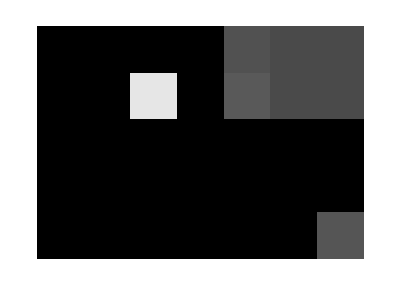

```mathematica
1-scoresImg//ArrayPlot
```

```mathematica
findPerimeter[space]
```

{{1,4},{1,7},{2,4},{2,7},{3,4},{3,7},{3,8},{3,9},{3,10},{4,4},{4,10},{5,1},{5,2},{5,3},{5,4},{5,10},{6,1},{6,2},{6,3},{6,4},{6,10},{7,4},{7,10},{8,4},{8,10},{9,4},{9,10},{10,4},{10,5},{10,6},{10,7},{10,8},{10,9},{10,10},{11,9},{11,10},{12,9},{12,10},{13,9},{13,10}}

```mathematica
Erosion[space,1]-Erosion[space,2]//ArrayPlot
```

-Graphics-

```mathematica
tile={{1,1,1},{0,0,1}}
```

{{1,1,1},{0,0,1}}

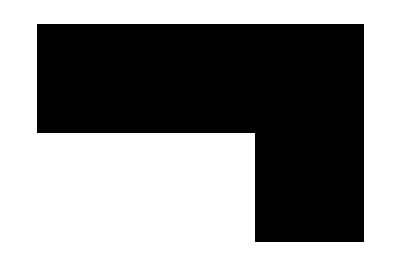

```mathematica
ArrayPlot[tile]
```

```mathematica
positionTile[tile,{2,2},{10,10}]+positionTile[tile,{2,4},{10,10}]//ArrayPlot
```

-Graphics-

```mathematica
Blur[1-Image[positionTile[tile,{2,2},{10,10}]+positionTile[tile,{2,4},{10,10}],"Bit"],2]
```

-Graphics-

```mathematica
positionTile[tile,{3,3},{10,10}]+positionTile[tile,{2,4},{10,10}]//ArrayPlot
```

-Graphics-

```mathematica
Blur[1-Image[positionTile[tile,{3,3},{10,10}]+positionTile[tile,{2,4},{10,10}],"Bit"],2]
```

-Graphics-

```mathematica
1-Min[ImageData[Blur[1-Image[positionTile[tile,{3,3},{10,10}]+positionTile[tile,{2,4},{10,10}],"Bit"],2]]]
```

0.741223

```mathematica
1-Min[ImageData[Blur[1-Image[positionTile[tile,{2,2},{10,10}]+positionTile[tile,{2,4},{10,10}],"Bit"],2]]]
```

0.588456

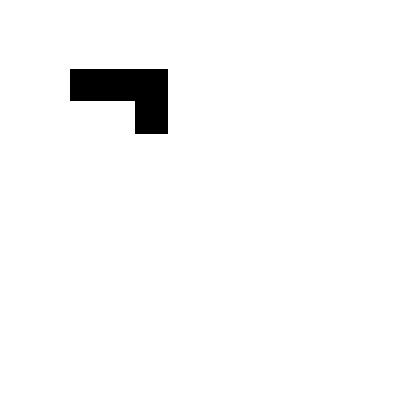

```mathematica
positionTile[tile,{2,2},{10,10}]//ArrayPlot
```

```mathematica
tile2={{1,1},{0,1},{0,1},{1,1}}
```

{{1,1},{0,1},{0,1},{1,1}}

```mathematica
tile2//ArrayPlot
```

-Graphics-

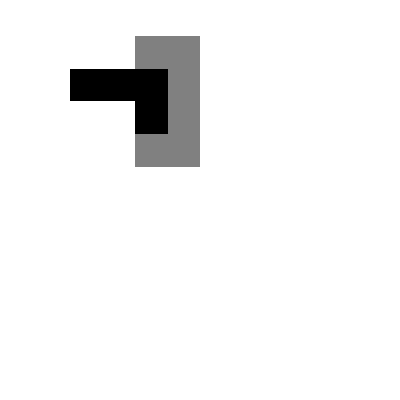

```mathematica
positionTile[tile,{2,2},{10,10}]+0.5*positionTile[tile2,{4,1},{10,10}]//ArrayPlot
```

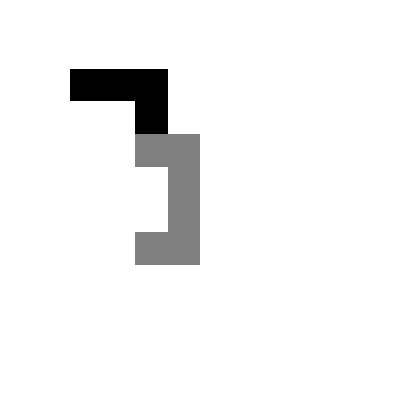

```mathematica
positionTile[tile,{2,2},{10,10}]+0.5*positionTile[tile2,{4,4},{10,10}]//ArrayPlot
```

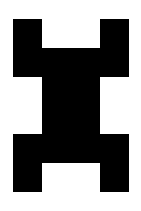

```mathematica
tile//ArrayPlot
```

```mathematica
tile//MatrixForm
```

(1 | 0 | 0 | 1
1 | 1 | 1 | 1
0 | 1 | 1 | 0
0 | 1 | 1 | 0
1 | 1 | 1 | 1
1 | 0 | 0 | 1)